# Efficiency Comparison Physics Data

Model-picking analysis for the LHC L1 anomaly-detection physics data: the validation strategies are compared across architectures by the test efficiency of the Pareto point each one selects, at two operating points -- the 250 Hz trigger tier (file suffix _250Hz) and the q = 0.99 quantile tier (suffix _q99).
Inputs: pareto_effs/<exp>.csv and <exp>_eval.csv harvested by scripts/analysis/harvest_pareto_effs.py, and Optuna front CSVs under paretos/physics/ from scripts/optuna/fetch_optuna_pareto.py. Figures are exported to effs/.
All methods live in notebooks/lib/ (effs_*.wl); this notebook holds only configuration, hand-transcribed legacy data, and drivers. Run it top-to-bottom (Evaluation > Evaluate Notebook), or headlessly via scripts/analysis/nb_run.wls.

## Setup

Load the shared method library and point it at the harvested Pareto-efficiency CSVs.

```mathematica
SetDirectory[NotebookDirectory[]];
Get[FileNameJoin[{NotebookDirectory[], "lib", #}]] & /@
  {"effs_data.wl", "effs_rules.wl", "effs_stats.wl", "effs_format.wl",
   "effs_tables.wl", "effs_style.wl", "effs_plots.wl"};
paretoEffsDir = "pareto_effs";
```

Five validation strategies compete to pick a model from each architecture's Pareto front: semi-supervised (CVaR25 of the signal efficiencies), stability (threshold drift), CAP, wasserstein (W1 distance) and consistency. The tables below define their canonical order, whether their objective is maximised, the Optuna study objective each maps to, display names, and box-plot colors.

```mathematica
strategyOrder = {"cvar25", "stability", "cap", "wasserstein", 
   "consistency"};
boxStrategyOrder = {"cvar25", "stability", "cap", "wasserstein", 
   "consistency"};
strategyMaximizeQ = <|"cvar25" -> True, "cvar10" -> True, 
   "cap" -> True, "stability" -> False, "wasserstein" -> False, 
   "consistency" -> True|>;
strategyStudyObj = <|"cvar25" -> "cvar25eff", "cvar10" -> "cvar10eff",
    "cap" -> "cap", "stability" -> "drift", 
   "wasserstein" -> "wasserstein", "consistency" -> "consistency"|>;
strategyPretty = <|"cvar25" -> "semi-supervised", 
   "cvar10" -> "semi-sup (CVaR10)", "cap" -> "CAP", 
   "stability" -> "stable", "wasserstein" -> "wasserstein", 
   "consistency" -> "consistency"|>;
strategyBoxColors = <|"cvar25" -> "#3f90da", "stability" -> "#ffa90e",
    "cap" -> "#bd1f01", "wasserstein" -> "#832db6", 
   "consistency" -> "#94a4a2"|>;
```

Domain configuration: which harvest experiment backs each architecture at each operating point, where the front CSVs live, and where figures land. DTE has no harvest CSV yet; rebuttalRuns notes it once and every table and plot simply omits it.

```mathematica
(*Domain configuration for the model-picking analysis.*)
rebuttalDomain = "physics";
rebuttalFrontsDir = "paretos/physics";
rebuttalOutDir = "effs/";
rebuttalTierSuffix = "_250Hz";
rebuttalModelExps = <|"AE" -> "physics_ae_pareto", 
   "VAE" -> "physics_vae_pareto", "DSAE" -> "physics_dsae_pareto", 
   "DSVAE" -> "physics_dsvae_pareto", "SVDD" -> "physics_svdd_pareto",
    "RealNVP" -> "physics_realnvp_pareto", 
   "DTE" -> "physics_dte_pareto"|>;
```

```mathematica
(*q99 experiment remap*)
rebuttalModelExpsQ99 = <|"AE" -> "physics_ae_q99_pareto", 
   "VAE" -> "physics_vae_q99_pareto", 
   "DSAE" -> "physics_dsae_q99_pareto", 
   "DSVAE" -> "physics_dsvae_q99_pareto", 
   "SVDD" -> "physics_svdd_q99_pareto", 
   "RealNVP" -> "physics_realnvp_q99_pareto", 
   "DTE" -> "physics_dte_q99_pareto"|>;
```

Fire-on-everything guard. Picks whose per-signal efficiencies are all ~100% (score collapse at the threshold, e.g. the SVDD semi-supervised picks) carry no selection information; the guard treats them like collapsed methods, so the mean renders as a dash and every column computed from the method (deltas, CIs, p-values and their Holm ranks) goes Missing -> dash.

The cut sits in a clean data gap: across all physics evaluations the degenerate cluster has min per-signal efficiency >= 99.78% (mean >= 99.96%) while genuine runs stay below 6.2% (mean <= 75.2%).

Every physics table is an efficiency table, so the guard is never switched off here; the cifar10/robustad notebooks disable it around their AUPRC tables, where a saturated column means perfect separation rather than a degenerate detector.

```mathematica
$degenerateGuard = True;
```

## Results

## Pareto Fronts

One row of Pareto-front scatter plots per architecture (grey = dominated trials, red = front), one panel per strategy. Exported as fronts_<model>_250Hz.

```mathematica
frontRowAE = modelFrontRow[rebuttalFrontsDir, "ae", "AE"]
Export[rebuttalOutDir <> "fronts_ae" <> rebuttalTierSuffix <> ".svg", frontRowAE, "SVG"];
Export[rebuttalOutDir <> "fronts_ae" <> rebuttalTierSuffix <> ".pdf", frontRowAE, "PDF"];
```

```mathematica
frontRowVAE = modelFrontRow[rebuttalFrontsDir, "vae", "VAE"]
Export[rebuttalOutDir <> "fronts_vae" <> rebuttalTierSuffix <> ".svg", frontRowVAE, "SVG"];
Export[rebuttalOutDir <> "fronts_vae" <> rebuttalTierSuffix <> ".pdf", frontRowVAE, "PDF"];
```

```mathematica
frontRowDSAE = modelFrontRow[rebuttalFrontsDir, "dsae", "DSAE"]
Export[rebuttalOutDir <> "fronts_dsae" <> rebuttalTierSuffix <> ".svg", frontRowDSAE, "SVG"];
Export[rebuttalOutDir <> "fronts_dsae" <> rebuttalTierSuffix <> ".pdf", frontRowDSAE, "PDF"];
```

```mathematica
frontRowDSVAE = modelFrontRow[rebuttalFrontsDir, "dsvae", "DSVAE"]
Export[rebuttalOutDir <> "fronts_dsvae" <> rebuttalTierSuffix <> ".svg", frontRowDSVAE, "SVG"];
Export[rebuttalOutDir <> "fronts_dsvae" <> rebuttalTierSuffix <> ".pdf", frontRowDSVAE, "PDF"];
```

```mathematica
frontRowSVDD = modelFrontRow[rebuttalFrontsDir, "svdd", "SVDD"]
Export[rebuttalOutDir <> "fronts_svdd" <> rebuttalTierSuffix <> ".svg", frontRowSVDD, "SVG"];
Export[rebuttalOutDir <> "fronts_svdd" <> rebuttalTierSuffix <> ".pdf", frontRowSVDD, "PDF"];
```

```mathematica
frontRowRealNVP = modelFrontRow[rebuttalFrontsDir, "realnvp", "RealNVP"]
Export[rebuttalOutDir <> "fronts_realnvp" <> rebuttalTierSuffix <> ".svg", frontRowRealNVP, "SVG"];
Export[rebuttalOutDir <> "fronts_realnvp" <> rebuttalTierSuffix <> ".pdf", frontRowRealNVP, "PDF"];
```

```mathematica
frontRowDTE = modelFrontRow[rebuttalFrontsDir, "dte", "DTE"]
Export[rebuttalOutDir <> "fronts_dte" <> rebuttalTierSuffix <> ".svg", frontRowDTE, "SVG"];
Export[rebuttalOutDir <> "fronts_dte" <> rebuttalTierSuffix <> ".pdf", frontRowDTE, "PDF"];
```

## Legacy Pareto Point Selection (by hand)

### 1. Tables

Hand-transcribed per-signal test efficiencies (%) of the original picks at both operating points; kept in-notebook as the provenance record for the published tables -- do not regenerate them mechanically. 250 Hz arrays are percent values; the q99 arrays were transcribed as fractions and carry an explicit *100.

#### 250 Hz Data

```mathematica
allArchitectures250hz = <|
   "AE" -> <|
     "semisupervised" -> {0.31, 0.53, 0.00, 0.17, 1.79, 1.05, 0.96, 
       17.05, 17.50, 21.16, 1.92, 0.06, 16.86, 15.76, 15.65, 7.14, 
       0.59, 0.33, 0.58, 17.41},
     "CAP" -> {0.18, 0.44, 0.00, 0.05, 0.98, 0.87, 0.98, 13.67, 14.24,
        18.44, 0.82, 0.04, 14.97, 13.93, 12.62, 3.82, 0.36, 0.41, 
       1.18, 16.67},
     "stable" -> {2.97, 0.39, 0.00, 0.14, 0.81, 0.67, 0.72, 9.52, 
       9.81, 14.43, 0.62, 0.04, 12.24, 9.46, 8.23, 2.84, 0.29, 0.30, 
       0.48, 11.91},
     "wasserstein" -> {0.16, 0.22, 0.00, 0.03, 0.77, 0.57, 0.66, 5.38,
        5.42, 14.82, 0.51, 0.02, 12.21, 5.47, 5.32, 2.45, 0.20, 0.18, 
       0.33, 9.64}
     |>,
   "VAE" -> <|
     "semisupervised" -> {0.02, 0.18, 0.00, 0.00, 0.77, 0.86, 1.02, 
       8.43, 8.88, 18.93, 0.68, 0.04, 12.44, 10.11, 9.15, 2.79, 0.32, 
       0.24, 0.38, 15.93},
     "CAP" -> {0.02, 0.20, 0.00, 0.00, 0.82, 0.93, 1.10, 8.87, 9.35, 
       19.74, 0.73, 0.04, 12.93, 10.70, 9.60, 2.93, 0.32, 0.24, 0.40, 
       16.83},
     "stable" -> {0.02, 0.19, 0.00, 0.01, 0.95, 1.03, 1.15, 6.34, 
       6.56, 21.12, 0.65, 0.04, 15.36, 8.08, 7.14, 2.34, 0.33, 0.21, 
       0.36, 15.90},
     "wasserstein" -> {0.02, 0.21, 0.00, 0.01, 0.91, 1.07, 1.17, 5.77,
        5.92, 23.70, 0.78, 0.04, 15.10, 7.62, 6.77, 2.76, 0.32, 0.12, 
       0.18, 17.37}
     |>,
   "DSAE" -> <|
     "semisupervised" -> {0.47, 0.59, 0.00, 0.10, 1.22, 1.04, 1.16, 
       24.23, 25.34, 17.00, 1.16, 0.05, 13.27, 21.69, 21.13, 6.43, 
       0.40, 0.60, 1.00, 19.04},
     "CAP" -> {0.39, 0.61, 0.00, 0.10, 1.23, 1.08, 1.20, 26.20, 26.86,
        20.58, 1.12, 0.05, 15.23, 23.61, 23.15, 6.91, 0.43, 0.68, 
       1.12, 20.36},
     "stable" -> {1.01, 0.33, 0.00, 0.04, 0.86, 0.56, 0.68, 6.52, 
       6.58, 14.04, 0.60, 0.02, 11.11, 5.88, 6.23, 2.13, 0.26, 0.73, 
       4.65, 9.09},
     "wasserstein" -> {0.15, 1.74, 0.00, 0.02, 1.04, 0.72, 0.84, 6.25,
        6.60, 15.32, 0.66, 0.03, 12.84, 6.37, 6.33, 2.67, 0.31, 0.47, 
       1.36, 11.24}
     |>,
   "DSVAE" -> <|
     "semisupervised" -> {0.11, 0.18, 0.00, 0.01, 1.18, 0.97, 1.12, 
       12.13, 12.89, 17.85, 0.77, 0.04, 14.00, 13.12, 11.79, 3.63, 
       0.38, 0.44, 0.76, 16.27},
     "CAP" -> {0.02, 0.19, 0.00, 0.01, 1.10, 1.02, 1.15, 9.51, 10.00, 
       19.45, 0.70, 0.04, 15.23, 11.09, 9.72, 3.16, 0.37, 0.27, 0.46, 
       16.87},
     "stable" -> {0.01, 0.55, 0.00, 0.01, 0.77, 1.02, 1.18, 9.01, 
       9.50, 20.08, 0.88, 0.04, 13.04, 11.17, 9.46, 2.67, 0.28, 0.21, 
       0.35, 16.81},
     "wasserstein" -> {0.05, 0.33, 0.00, 0.01, 0.31, 0.15, 0.13, 1.40,
        1.53, 3.99, 0.32, 0.02, 2.41, 0.91, 1.21, 1.28, 0.11, 0.03, 
       0.05, 1.85}
     |>,
   "SVDD" -> <|
     "semisupervised" -> {0.44, 0.14, 0.00, 1.01, 0.90, 0.72, 0.78, 
       5.23, 4.75, 16.16, 0.67, 0.04, 11.13, 5.35, 5.70, 2.29, 0.24, 
       0.24, 0.65, 9.50},
     "CAP" -> {1.14, 0.19, 0.00, 0.05, 0.71, 0.68, 0.81, 9.06, 9.21, 
       13.26, 0.83, 0.03, 10.59, 8.88, 8.48, 2.99, 0.27, 0.44, 0.72, 
       12.24},
     "stable" -> {0.50, 0.19, 0.01, 0.11, 1.09, 0.69, 0.58, 8.81, 
       8.89, 8.40, 1.93, 0.05, 8.41, 7.73, 7.50, 6.27, 0.37, 0.05, 
       0.06, 9.61},
     "wasserstein" -> {0.71, 0.09, 0.00, 0.03, 0.55, 0.46, 0.58, 7.57,
        7.98, 13.30, 0.38, 0.02, 9.92, 6.44, 6.05, 1.91, 0.20, 0.09, 
       0.14, 8.63}
     |>,
   "RealNVP" -> <|
     "semisupervised" -> {1.13, 0.15, 0.02, 0.20, 1.07, 0.77, 0.90, 
       11.70, 12.06, 13.67, 0.93, 0.07, 10.29, 10.45, 10.66, 3.46, 
       0.41, 1.95, 9.18, 11.67},
     "CAP" -> {2.55, 0.04, 0.00, 0.71, 0.49, 0.31, 0.28, 12.71, 12.80,
        3.98, 0.61, 0.06, 3.86, 9.81, 8.85, 2.87, 0.19, 0.16, 0.39, 
       4.59},
     "stable" -> {1.47, 0.04, 0.00, 0.17, 0.34, 0.36, 0.37, 12.19, 
       12.77, 3.79, 0.54, 0.04, 4.60, 9.92, 8.83, 2.26, 0.14, 0.15, 
       0.23, 5.09},
     "wasserstein" -> {0.99, 0.02, 0.00, 0.58, 0.18, 0.19, 0.21, 6.25,
        6.29, 1.99, 0.25, 0.04, 2.19, 5.28, 4.72, 1.15, 0.13, 0.08, 
       0.16, 2.50}
     |>
   |>;
   
compactTableTex = 
  BuildLatexTableCompactAsymCollapse[allArchitectures250hz, 10000, 
   0.05, 2];
printTable[compactTableTex];
printTable[BuildMarkdownTableCompactAsymCollapse[allArchitectures250hz, 
   10000, 0.05, 2]];
```

\begin{tabular}{lccccccccccc}
\toprule
Arch. & Semi & CAP & Cons & Stable & W1 & CAP$-$Cons & $p$ & CAP$-$Stable & $p$ & CAP$-$W1 & $p$ \\
\midrule
AE & 6.84 & 5.73 & coll & 4.29 & 3.22 & n/a & n/a & $1.44^{+0.95}_{-0.91}$ & 0.007 & $2.52^{+1.51}_{-1.39}$ & <0.001 \\
VAE & 4.56 & 4.79 & coll & 4.39 & 4.49 & n/a & n/a & $0.40^{+0.58}_{-0.54}$ & 0.629 & $0.30^{+0.76}_{-0.75}$ & 0.659 \\
DSAE & 7.80 & 8.55 & coll & 3.57 & 3.75 & n/a & n/a & $4.98^{+3.45}_{-3.09}$ & 0.014 & $4.80^{+3.39}_{-2.98}$ & 0.007 \\
DSVAE & 5.38 & 5.02 & coll & 4.85 & 0.80 & n/a & n/a & $0.17^{+0.26}_{-0.20}$ & 0.629 & $4.21^{+2.50}_{-2.25}$ & <0.001 \\
SVDD & 3.30 & 4.03 & coll & 3.56 & 3.25 & n/a & n/a & $0.47^{+0.70}_{-0.64}$ & 0.603 & $0.78^{+0.47}_{-0.40}$ & <0.001 \\
RealNVP & 5.04 & 3.26 & coll & 3.17 & 1.66 & n/a & n/a & $0.10^{+0.17}_{-0.16}$ & 0.629 & $1.60^{+0.97}_{-0.85}$ & <0.001 \\
\bottomrule
\end{tabular}
% legend: no-pick = rule could not select from this front (knee needs >= 3 Pareto points, best-Q' needs >= 1); coll = method collapsed (all-zero) or excluded by the saturation guard; n/a = comparison not computable (a required side is missing).

| Arch. | Semi | CAP | Cons | Stable | W1 | CAP-Cons | p | CAP-Stable | p | CAP-W1 | p |
|---|---|---|---|---|---|---|---|---|---|---|---|
| AE | 6.84 | 5.73 | coll | 4.29 | 3.22 | n/a | n/a | $1.44^{+0.95}_{-0.93}$ | 0.007 | $2.52^{+1.51}_{-1.39}$ | <0.001 |
| VAE | 4.56 | 4.79 | coll | 4.39 | 4.49 | n/a | n/a | $0.40^{+0.57}_{-0.55}$ | 0.629 | $0.30^{+0.74}_{-0.75}$ | 0.659 |
| DSAE | 7.80 | 8.55 | coll | 3.57 | 3.75 | n/a | n/a | $4.98^{+3.41}_{-3.08}$ | 0.014 | $4.80^{+3.35}_{-2.96}$ | 0.007 |
| DSVAE | 5.38 | 5.02 | coll | 4.85 | 0.80 | n/a | n/a | $0.17^{+0.27}_{-0.20}$ | 0.629 | $4.21^{+2.51}_{-2.28}$ | <0.001 |
| SVDD | 3.30 | 4.03 | coll | 3.56 | 3.25 | n/a | n/a | $0.47^{+0.69}_{-0.64}$ | 0.603 | $0.78^{+0.46}_{-0.40}$ | <0.001 |
| RealNVP | 5.04 | 3.26 | coll | 3.17 | 1.66 | n/a | n/a | $0.10^{+0.17}_{-0.16}$ | 0.629 | $1.60^{+0.96}_{-0.83}$ | <0.001 |

legend: no-pick = rule could not select from this front (knee needs >= 3 Pareto points, best-Q' needs >= 1); coll = method collapsed (all-zero) or excluded by the saturation guard; n/a = comparison not computable (a required side is missing).

#### Q99 Data

```mathematica
allArchitecturesQ99 = <|
   "AE" ->
    <|
     "semisupervised" -> {42.88, 29.50, 1.79, 28.03, 70.93, 62.94, 
       64.11, 97.41, 97.81, 89.64, 81.17, 16.64, 72.94, 95.56, 96.39, 
       87.72, 38.59, 74.33, 85.60, 99.20},
     "CAP" -> {39.15, 17.96, 2.45, 24.93, 63.18, 60.75, 62.76, 97.66, 
       97.99, 89.29, 80.69, 15.57, 72.04, 96.50, 96.50, 86.07, 31.32, 
       69.21, 81.74, 99.22},
     "stable" -> {42.02, 25.64, 1.86, 25.51, 72.09, 67.16, 69.69, 
       97.68, 98.08, 91.25, 85.01, 17.41, 75.34, 96.32, 96.52, 87.75, 
       38.47, 75.25, 86.08, 99.48},
     "wasserstein" -> {36.12, 13.92, 2.05, 29.49, 58.33, 56.12, 59.11,
        96.90, 97.38, 85.85, 72.07, 13.80, 67.73, 95.52, 95.43, 81.77,
        26.28, 65.96, 78.85, 97.81}
     |>,
   "VAE" ->
    <|
     "semisupervised" -> {52.97, 29.83, 1.13, 37.04, 77.87, 68.88, 
       72.95, 99.27, 99.40, 93.33, 91.35, 24.73, 80.01, 98.87, 98.92, 
       94.89, 55.58, 85.09, 92.09, 99.82},
     "CAP" -> {51.20, 29.65, 1.42, 28.61, 80.22, 72.93, 76.38, 99.62, 
       99.70, 94.01, 92.30, 31.04, 81.48, 99.42, 99.43, 96.44, 58.54, 
       85.76, 92.50, 99.77},
     "stable" -> {28.53, 12.95, 0.94, 4.31, 66.47, 58.22, 62.85, 
       96.64, 96.97, 91.61, 88.13, 18.55, 76.63, 96.29, 97.04, 90.42, 
       42.93, 79.82, 88.57, 99.47},
     "wasserstein" -> {32.07, 13.91, 1.10, 5.54, 66.34, 58.47, 62.83, 
       98.64, 98.81, 91.65, 88.16, 20.70, 77.14, 98.23, 98.31, 92.34, 
       45.69, 82.22, 89.71, 99.45}
     |>,
   "DSAE" -> <|
     "semisupervised" -> {39.85, 33.24, 1.66, 29.69, 69.31, 61.43, 
       64.87, 98.20, 98.52, 90.27, 84.07, 15.58, 73.85, 97.01, 97.35, 
       89.51, 38.35, 75.79, 86.89, 99.59},
     "CAP" -> {32.00, 13.64, 2.12, 19.83, 56.61, 51.48, 54.60, 95.83, 
       96.38, 85.91, 73.04, 10.89, 67.00, 93.80, 94.04, 79.84, 24.74, 
       57.40, 73.84, 98.15},
     "stable" -> {34.29, 12.32, 1.99, 21.52, 54.37, 49.06, 51.85, 
       96.70, 97.19, 85.84, 73.32, 10.52, 67.07, 94.97, 95.06, 80.25, 
       23.81, 64.76, 77.33, 98.33},
     "wasserstein" -> {35.19, 15.12, 1.70, 23.24, 56.07, 49.45, 52.75,
        96.41, 96.94, 87.46, 77.44, 10.62, 69.12, 94.64, 94.82, 80.69,
        26.15, 66.53, 79.65, 98.80}
     |>,
   "DSVAE" -> <|
     "semisupervised" -> {54.88, 30.67, 1.47, 43.45, 79.62, 73.19, 
       77.08, 99.58, 99.65, 94.27, 92.70, 30.04, 81.86, 99.37, 99.36, 
       96.15, 58.67, 85.27, 92.34, 99.81},
     "CAP" -> {55.71, 30.01, 1.37, 38.88, 80.55, 73.49, 77.67, 99.42, 
       99.53, 94.15, 92.66, 27.94, 81.29, 99.13, 99.18, 95.76, 59.44, 
       87.15, 93.29, 99.84},
     "stable" -> {38.46, 34.41, 1.51, 44.53, 56.00, 52.41, 49.99, 
       97.32, 97.43, 89.88, 84.81, 26.61, 74.31, 96.91, 96.94, 88.38, 
       37.00, 36.53, 62.19, 98.82},
     "wasserstein" -> {34.39, 23.17, 1.09, 10.98, 51.54, 43.86, 42.55,
        89.02, 88.64, 86.88, 77.23, 11.85, 68.69, 88.09, 89.38, 77.90,
        28.50, 56.26, 76.71, 97.38}
     |>,
   "SVDD" -> <|
     "semisupervised" -> {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 
       0., 0., 0., 0., 0., 0., 0., 0., 0.},
     "CAP" -> {31.14, 7.99, 1.14, 5.04, 58.28, 51.71, 55.04, 97.46, 
       97.75, 89.59, 84.23, 14.31, 73.29, 96.81, 97.03, 87.95, 32.81, 
       73.76, 84.11, 99.40},
     "stable" -> {43.72, 16.03, 1.99, 17.61, 67.25, 61.34, 66.32, 
       95.99, 96.42, 91.01, 86.48, 19.04, 75.83, 95.29, 95.21, 86.91, 
       44.13, 81.72, 89.96, 99.44},
     "wasserstein" -> {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.,
        0., 0., 0., 0., 0., 0., 0., 0.}
     |>,
   "RealNVP" -> <|
     "semisupervised" -> {56.09, 18.69, 1.70, 48.78, 81.25, 76.74, 
       79.52, 99.64, 99.69, 94.13, 92.36, 27.38, 80.96, 99.37, 99.32, 
       95.63, 53.18, 83.01, 91.76, 99.81},
     "CAP" -> {15.69, 0.93, 2.95, 20.13, 26.50, 27.59, 27.41, 88.25, 
       88.59, 43.85, 27.29, 12.19, 35.05, 83.07, 82.14, 56.58, 15.34, 
       19.89, 26.28, 57.32},
     "stable" -> {20.54, 0.87, 2.43, 23.64, 23.86, 23.78, 22.93, 
       85.05, 85.16, 41.03, 25.09, 11.07, 33.36, 78.36, 78.00, 52.98, 
       14.30, 22.98, 34.02, 52.36},
     "wasserstein" -> {17.88, 1.34, 1.93, 23.86, 20.34, 21.50, 20.52, 
       85.52, 85.73, 39.47, 23.39, 9.91, 32.17, 79.78, 78.59, 51.93, 
       12.24, 15.57, 18.99, 52.27}
     |>
   |>;
```

```mathematica
compactTableTex = 
  BuildLatexTableCompactAsymCollapse[allArchitecturesQ99, 10000, 0.05,
    2];
printTable[compactTableTex];
printTable[BuildMarkdownTableCompactAsymCollapse[allArchitecturesQ99, 
   10000, 0.05, 2]];
```

### 2. Plots

CMS-style box plots of the same hand-transcribed arrays, one panel per architecture and operating point, exported as <model>_<tier>.{svg,pdf,jpeg}. The data cells below feed the single driver at the end; the model badge position is the only per-panel parameter (the SVDD badge sits lower at 250 Hz to clear the whiskers).

```mathematica
legacyEffs["ae", "250Hz"] = <|
  "semisupervised" -> {0.31, 0.53, 0., 0.17, 1.79, 1.05, 0.96, 17.05, 17.5, 21.16, 1.92, 0.06, 16.86, 15.76, 15.65, 7.14, 0.59, 0.33, 0.58, 17.41},
  "CAP" -> {0.18, 0.44, 0., 0.05, 0.98, 0.87, 0.98, 13.67, 14.24, 18.44, 0.82, 0.04, 14.97, 13.93, 12.62, 3.82, 0.36, 0.41, 1.18, 16.67},
  "stable" -> {2.97, 0.39, 0., 0.14, 0.81, 0.67, 0.72, 9.52, 9.81, 14.43, 0.62, 0.04, 12.24, 9.46, 8.23, 2.84, 0.29, 0.3, 0.48, 11.91},
  "wasserstein" -> {0.16, 0.22, 0., 0.03, 0.77, 0.57, 0.66, 5.38, 5.42, 14.82, 0.51, 0.02, 12.21, 5.47, 5.32, 2.45, 0.2, 0.18, 0.33, 9.64}
|>;
```

```mathematica
legacyEffs["ae", "q99"] = <|
  "semisupervised" -> {0.4288, 0.295, 0.0179, 0.2803, 0.7093, 0.6294, 0.6411, 0.9741, 0.9781, 0.8964, 0.8117, 0.1664, 0.7294, 0.9556, 0.9639, 0.8772, 0.3859, 0.7433, 0.856, 0.992}*100,
  "CAP" -> {0.3915, 0.1796, 0.0245, 0.2493, 0.6318, 0.6075, 0.6276, 0.9766, 0.9799, 0.8929, 0.8069, 0.1557, 0.7204, 0.965, 0.965, 0.8607, 0.3132, 0.6921, 0.8174, 0.9922}*100,
  "stable" -> {0.4202, 0.2564, 0.0186, 0.2551, 0.7209, 0.6716, 0.6969, 0.9768, 0.9808, 0.9125, 0.8501, 0.1741, 0.7534, 0.9632, 0.9652, 0.8775, 0.3847, 0.7525, 0.8608, 0.9948}*100,
  "wasserstein" -> {0.3612, 0.1392, 0.0205, 0.2949, 0.5833, 0.5612, 0.5911, 0.969, 0.9738, 0.8585, 0.7207, 0.138, 0.6773, 0.9552, 0.9543, 0.8177, 0.2628, 0.6596, 0.7885, 0.9781}*100
|>;
```

```mathematica
legacyEffs["vae", "250Hz"] = <|
  "semisupervised" -> {0.02, 0.18, 0., 0., 0.77, 0.86, 1.02, 8.43, 8.88, 18.93, 0.68, 0.04, 12.44, 10.11, 9.15, 2.79, 0.32, 0.24, 0.38, 15.93},
  "CAP" -> {0.02, 0.2, 0., 0., 0.82, 0.93, 1.1, 8.87, 9.35, 19.74, 0.73, 0.04, 12.93, 10.7, 9.6, 2.93, 0.32, 0.24, 0.4, 16.83},
  "stable" -> {0.02, 0.19, 0., 0.01, 0.95, 1.03, 1.15, 6.34, 6.56, 21.12, 0.65, 0.04, 15.36, 8.08, 7.14, 2.34, 0.33, 0.21, 0.36, 15.9},
  "wasserstein" -> {0.02, 0.21, 0., 0.01, 0.91, 1.07, 1.17, 5.77, 5.92, 23.7, 0.78, 0.04, 15.1, 7.62, 6.77, 2.76, 0.32, 0.12, 0.18, 17.37}
|>;
```

```mathematica
legacyEffs["vae", "q99"] = <|
  "semisupervised" -> {0.5297, 0.2983, 0.0113, 0.3704, 0.7787, 0.6888, 0.7295, 0.9927, 0.994, 0.9333, 0.9135, 0.2473, 0.8001, 0.9887, 0.9892, 0.9489, 0.5558, 0.8509, 0.9209, 0.9982}*100,
  "CAP" -> {0.512, 0.2965, 0.0142, 0.2861, 0.8022, 0.7293, 0.7638, 0.9962, 0.997, 0.9401, 0.923, 0.3104, 0.8148, 0.9942, 0.9943, 0.9644, 0.5854, 0.8576, 0.925, 0.9977}*100,
  "stable" -> {0.2853, 0.1295, 0.0094, 0.0431, 0.6647, 0.5822, 0.6285, 0.9664, 0.9697, 0.9161, 0.8813, 0.1855, 0.7663, 0.9629, 0.9704, 0.9042, 0.4293, 0.7982, 0.8857, 0.9947}*100,
  "wasserstein" -> {0.3207, 0.1391, 0.011, 0.0554, 0.6634, 0.5847, 0.6283, 0.9864, 0.9881, 0.9165, 0.8816, 0.207, 0.7714, 0.9823, 0.9831, 0.9234, 0.4569, 0.8222, 0.8971, 0.9945}*100
|>;
```

```mathematica
legacyEffs["dsae", "250Hz"] = <|
  "semisupervised" -> {0.47, 0.59, 0., 0.1, 1.22, 1.04, 1.16, 24.23, 25.34, 17., 1.16, 0.05, 13.27, 21.69, 21.13, 6.43, 0.4, 0.6, 1., 19.04},
  "CAP" -> {0.39, 0.61, 0., 0.1, 1.23, 1.08, 1.2, 26.2, 26.86, 20.58, 1.12, 0.05, 15.23, 23.61, 23.15, 6.91, 0.43, 0.68, 1.12, 20.36},
  "stable" -> {1.01, 0.33, 0., 0.04, 0.86, 0.56, 0.68, 6.52, 6.58, 14.04, 0.6, 0.02, 11.11, 5.88, 6.23, 2.13, 0.26, 0.73, 4.65, 9.09},
  "wasserstein" -> {0.15, 1.74, 0., 0.02, 1.04, 0.72, 0.84, 6.25, 6.6, 15.32, 0.66, 0.03, 12.84, 6.37, 6.33, 2.67, 0.31, 0.47, 1.36, 11.24}
|>;
```

```mathematica
legacyEffs["dsae", "q99"] = <|
  "semisupervised" -> {39.85, 33.24, 1.66, 29.69, 69.31, 61.43, 64.87, 98.2, 98.52, 90.27, 84.07, 15.58, 73.85, 97.01, 97.35, 89.51, 38.35, 75.79, 86.89, 99.59},
  "CAP" -> {32., 13.64, 2.12, 19.83, 56.61, 51.48, 54.6, 95.83, 96.38, 85.91, 73.04, 10.89, 67., 93.8, 94.04, 79.84, 24.74, 57.4, 73.84, 98.15},
  "stable" -> {34.29, 12.32, 1.99, 21.52, 54.37, 49.06, 51.85, 96.7, 97.19, 85.84, 73.32, 10.52, 67.07, 94.97, 95.06, 80.25, 23.81, 64.76, 77.33, 98.33},
  "wasserstein" -> {35.19, 15.12, 1.7, 23.24, 56.07, 49.45, 52.75, 96.41, 96.94, 87.46, 77.44, 10.62, 69.12, 94.64, 94.82, 80.69, 26.15, 66.53, 79.65, 98.8}
|>;
```

```mathematica
legacyEffs["dsvae", "250Hz"] = <|
  "semisupervised" -> {0.11, 0.18, 0., 0.01, 1.18, 0.97, 1.12, 12.13, 12.89, 17.85, 0.77, 0.04, 14., 13.12, 11.79, 3.63, 0.38, 0.44, 0.76, 16.27},
  "CAP" -> {0.02, 0.19, 0., 0.01, 1.1, 1.02, 1.15, 9.51, 10., 19.45, 0.7, 0.04, 15.23, 11.09, 9.72, 3.16, 0.37, 0.27, 0.46, 16.87},
  "stable" -> {0.01, 0.55, 0., 0.01, 0.77, 1.02, 1.18, 9.01, 9.5, 20.08, 0.88, 0.04, 13.04, 11.17, 9.46, 2.67, 0.28, 0.21, 0.35, 16.81},
  "wasserstein" -> {0.05, 0.33, 0., 0.01, 0.31, 0.15, 0.13, 1.4, 1.53, 3.99, 0.32, 0.02, 2.41, 0.91, 1.21, 1.28, 0.11, 0.03, 0.05, 1.85}
|>;
```

```mathematica
legacyEffs["dsvae", "q99"] = <|
  "semisupervised" -> {54.88, 30.67, 1.47, 43.45, 79.62, 73.19, 77.08, 99.58, 99.65, 94.27, 92.7, 30.04, 81.86, 99.37, 99.36, 96.15, 58.67, 85.27, 92.34, 99.81},
  "CAP" -> {55.71, 30.01, 1.37, 38.88, 80.55, 73.49, 77.67, 99.42, 99.53, 94.15, 92.66, 27.94, 81.29, 99.13, 99.18, 95.76, 59.44, 87.15, 93.29, 99.84},
  "stable" -> {38.46, 34.41, 1.51, 44.53, 56., 52.41, 49.99, 97.32, 97.43, 89.88, 84.81, 26.61, 74.31, 96.91, 96.94, 88.38, 37., 36.53, 62.19, 98.82},
  "wasserstein" -> {34.39, 23.17, 1.09, 10.98, 51.54, 43.86, 42.55, 89.02, 88.64, 86.88, 77.23, 11.85, 68.69, 88.09, 89.38, 77.9, 28.5, 56.26, 76.71, 97.38}
|>;
```

```mathematica
legacyEffs["svdd", "250Hz"] = <|
  "semisupervised" -> {0.44, 0.14, 0., 1.01, 0.9, 0.72, 0.78, 5.23, 4.75, 16.16, 0.67, 0.04, 11.13, 5.35, 5.7, 2.29, 0.24, 0.24, 0.65, 9.5},
  "CAP" -> {1.14, 0.19, 0., 0.05, 0.71, 0.68, 0.81, 9.06, 9.21, 13.26, 0.83, 0.03, 10.59, 8.88, 8.48, 2.99, 0.27, 0.44, 0.72, 12.24},
  "stable" -> {0.5, 0.19, 0.01, 0.11, 1.09, 0.69, 0.58, 8.81, 8.89, 8.4, 1.93, 0.05, 8.41, 7.73, 7.5, 6.27, 0.37, 0.05, 0.06, 9.61},
  "wasserstein" -> {0.71, 0.09, 0., 0.03, 0.55, 0.46, 0.58, 7.57, 7.98, 13.3, 0.38, 0.02, 9.92, 6.44, 6.05, 1.91, 0.2, 0.09, 0.14, 8.63}
|>;
```

```mathematica
legacyEffs["svdd", "q99"] = <|
  "semisupervised" -> {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.},
  "CAP" -> {0.3114, 0.0799, 0.0114, 0.0504, 0.5828, 0.5171, 0.5504, 0.9746, 0.9775, 0.8959, 0.8423, 0.1431, 0.7329, 0.9681, 0.9703, 0.8795, 0.3281, 0.7376, 0.8411, 0.994}*100,
  "stable" -> {0.4372, 0.1603, 0.0199, 0.1761, 0.6725, 0.6134, 0.6632, 0.9599, 0.9642, 0.9101, 0.8648, 0.1904, 0.7583, 0.9529, 0.9521, 0.8691, 0.4413, 0.8172, 0.8996, 0.9944}*100,
  "wasserstein" -> {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}
|>;
```

```mathematica
legacyEffs["realnvp", "250Hz"] = <|
  "semisupervised" -> {1.13, 0.15, 0.02, 0.2, 1.07, 0.77, 0.9, 11.7, 12.06, 13.67, 0.93, 0.07, 10.29, 10.45, 10.66, 3.46, 0.41, 1.95, 9.18, 11.67},
  "CAP" -> {2.55, 0.04, 0., 0.71, 0.49, 0.31, 0.28, 12.71, 12.8, 3.98, 0.61, 0.06, 3.86, 9.81, 8.85, 2.87, 0.19, 0.16, 0.39, 4.59},
  "stable" -> {1.47, 0.04, 0., 0.17, 0.34, 0.36, 0.37, 12.19, 12.77, 3.79, 0.54, 0.04, 4.6, 9.92, 8.83, 2.26, 0.14, 0.15, 0.23, 5.09},
  "wasserstein" -> {0.99, 0.02, 0., 0.58, 0.18, 0.19, 0.21, 6.25, 6.29, 1.99, 0.25, 0.04, 2.19, 5.28, 4.72, 1.15, 0.13, 0.08, 0.16, 2.5}
|>;
```

```mathematica
legacyEffs["realnvp", "q99"] = <|
  "semisupervised" -> {0.5609, 0.1869, 0.017, 0.4878, 0.8125, 0.7674, 0.7952, 0.9964, 0.9969, 0.9413, 0.9236, 0.2738, 0.8096, 0.9937, 0.9932, 0.9563, 0.5318, 0.8301, 0.9176, 0.9981}*100,
  "CAP" -> {0.1569, 0.0093, 0.0295, 0.2013, 0.265, 0.2759, 0.2741, 0.8825, 0.8859, 0.4385, 0.2729, 0.1219, 0.3505, 0.8307, 0.8214, 0.5658, 0.1534, 0.1989, 0.2628, 0.5732}*100,
  "stable" -> {0.2054, 0.0087, 0.0243, 0.2364, 0.2386, 0.2378, 0.2293, 0.8505, 0.8516, 0.4103, 0.2509, 0.1107, 0.3336, 0.7836, 0.78, 0.5298, 0.143, 0.2298, 0.3402, 0.5236}*100,
  "wasserstein" -> {0.1788, 0.0134, 0.0193, 0.2386, 0.2034, 0.215, 0.2052, 0.8552, 0.8573, 0.3947, 0.2339, 0.0991, 0.3217, 0.7978, 0.7859, 0.5193, 0.1224, 0.1557, 0.1899, 0.5227}*100
|>;
```

```mathematica
legacyModelLabel = <|"ae" -> "AE", "vae" -> "VAE", "dsae" -> "DSAE",
   "dsvae" -> "DSVAE", "svdd" -> "SVDD", "realnvp" -> "RealNVP"|>;
legacyLabelPos = <|
   {"ae", "250Hz"} -> {0.639, 0.899},
   {"ae", "q99"} -> {0.639, 0.899},
   {"vae", "250Hz"} -> {0.151, 0.899},
   {"vae", "q99"} -> {0.151, 0.899},
   {"dsae", "250Hz"} -> {0.639, 0.899},
   {"dsae", "q99"} -> {0.639, 0.899},
   {"dsvae", "250Hz"} -> {0.186, 0.899},
   {"dsvae", "q99"} -> {0.186, 0.899},
   {"svdd", "250Hz"} -> {0.17, 0.81},
   {"svdd", "q99"} -> {0.17, 0.9},
   {"realnvp", "250Hz"} -> {0.639, 0.899},
   {"realnvp", "q99"} -> {0.639, 0.899}|>;
```

```mathematica
Do[Module[{d = legacyEffs[m, tier], plot},
   plot = makeBoxCMS[
     Lookup[d, {"semisupervised", "stable", "CAP", "wasserstein"}],
     {"semi-supervised", "stable", "CAP", "wasserstein"},
     "Efficiency (%)", {0.085, 0.9}, {0.64, 0.9}, 1, 0.17,
     legacyModelLabel[m], legacyLabelPos[{m, tier}]];
   Export["effs/" <> m <> "_" <> tier <> "." <> ToLowerCase[#],
      plot, #] & /@ {"SVG", "PDF", "JPEG"}],
  {m, {"ae", "vae", "dsae", "dsvae", "svdd", "realnvp"}},
  {tier, {"250Hz", "q99"}}]
```

### 3. Quantile Comparison

Axis 1: both operating points side by side; the Holm family is per operating point, consistent with the main tables.

```mathematica
printTable[QuantileAxisLatex[allArchitectures250hz, allArchitecturesQ99]];
printTable[QuantileAxisMarkdown[allArchitectures250hz, allArchitecturesQ99]];
```

## Best Q'

Rule: from each front, take the retrained point whose recomputed strategy objective Q' is best. Tables carry bootstrap CIs and Holm-adjusted Wilcoxon p-values; the grid exports as grouped_bestq_250Hz. The quantile comparison applies the rule independently to the 250 Hz and q99 campaigns (disjoint trial sets from their own searches).

#### 250 Hz

```mathematica
bestqGroups = rulePickArrays[rebuttalModelExps, bestQPick];
bestqTabRows = HolmAdjustRows[BuildArchitectureRowsCompactCollapse[toLegacyGroups[bestqGroups], 10000, 0.05]];
printTable[LatexTableFromRows[bestqTabRows, 2]];
printTable[MarkdownTableFromRows[bestqTabRows, 2]];
```

note: no harvest CSV for physics_dte_pareto -- omitting this model.

\begin{tabular}{lcccccccc}
\toprule
Arch. & Semi & CAP & Stable & W1 & CAP$-$Stable & $p$ & CAP$-$W1 & $p$ \\
\midrule
AE & 6.58 & 5.87 & 2.02 & 3.43 & 2.89 & $3.85^{+2.11}_{-1.92}$ & <0.001 & $2.44^{+1.37}_{-1.28}$ & 0.002 & $2.98^{+1.60}_{-1.54}$ & <0.001 \\
VAE & 4.94 & 4.73 & 4.72 & 3.77 & 4.72 & $0.01^{+0.01}_{-0.01}$ & 0.001 & $0.96^{+0.75}_{-0.65}$ & 0.064 & $0.01^{+0.17}_{-0.15}$ & 1.000 \\
DSAE & 7.96 & 7.67 & 2.92 & 4.65 & 3.85 & $4.75^{+3.37}_{-2.91}$ & 0.005 & $3.02^{+1.85}_{-1.70}$ & 0.002 & $3.82^{+3.02}_{-2.58}$ & 0.083 \\
DSVAE & 3.74 & 3.29 & 4.80 & 0.01 & 0.93 & $-1.52^{+1.53}_{-1.94}$ & 0.455 & $3.28^{+2.11}_{-1.82}$ & <0.001 & $2.36^{+1.97}_{-1.70}$ & 0.085 \\
SVDD & coll & 4.37 & 6.69 & 3.56 & 10.07 & $-2.31^{+1.86}_{-2.30}$ & 0.840 & $0.82^{+0.96}_{-0.86}$ & 0.455 & $-5.70^{+2.99}_{-3.28}$ & <0.001 \\
RealNVP & 5.10 & 2.25 & 5.52 & 2.24 & 1.95 & $-3.27^{+1.79}_{-2.01}$ & <0.001 & $0.01^{+0.62}_{-0.62}$ & 1.000 & $0.31^{+0.95}_{-0.85}$ & 1.000 \\
\bottomrule
\end{tabular}
% legend: no-pick = rule could not select from this front (knee needs >= 3 Pareto points, best-Q' needs >= 1); coll = method collapsed (all-zero) or excluded by the saturation guard; n/a = comparison not computable (a required side is missing).

| Arch. | Semi | CAP | Stable | W1 | CAP-Stable | p | CAP-W1 | p |
|---|---|---|---|---|---|---|---|---|
| AE | 6.58 | 5.87 | 2.02 | 3.43 | 2.89 | $3.85^{+2.11}_{-1.92}$ | <0.001 | $2.44^{+1.37}_{-1.28}$ | 0.002 | $2.98^{+1.60}_{-1.54}$ | <0.001 |
| VAE | 4.94 | 4.73 | 4.72 | 3.77 | 4.72 | $0.01^{+0.01}_{-0.01}$ | 0.001 | $0.96^{+0.75}_{-0.65}$ | 0.064 | $0.01^{+0.17}_{-0.15}$ | 1.000 |
| DSAE | 7.96 | 7.67 | 2.92 | 4.65 | 3.85 | $4.75^{+3.37}_{-2.91}$ | 0.005 | $3.02^{+1.85}_{-1.70}$ | 0.002 | $3.82^{+3.02}_{-2.58}$ | 0.083 |
| DSVAE | 3.74 | 3.29 | 4.80 | 0.01 | 0.93 | $-1.52^{+1.53}_{-1.94}$ | 0.455 | $3.28^{+2.11}_{-1.82}$ | <0.001 | $2.36^{+1.97}_{-1.70}$ | 0.085 |
| SVDD | coll | 4.37 | 6.69 | 3.56 | 10.07 | $-2.31^{+1.86}_{-2.30}$ | 0.840 | $0.82^{+0.96}_{-0.86}$ | 0.455 | $-5.70^{+2.99}_{-3.28}$ | <0.001 |
| RealNVP | 5.10 | 2.25 | 5.52 | 2.24 | 1.95 | $-3.27^{+1.79}_{-2.01}$ | <0.001 | $0.01^{+0.62}_{-0.62}$ | 1.000 | $0.31^{+0.95}_{-0.85}$ | 1.000 |

legend: no-pick = rule could not select from this front (knee needs >= 3 Pareto points, best-Q' needs >= 1); coll = method collapsed (all-zero) or excluded by the saturation guard; n/a = comparison not computable (a required side is missing).

#### Plots

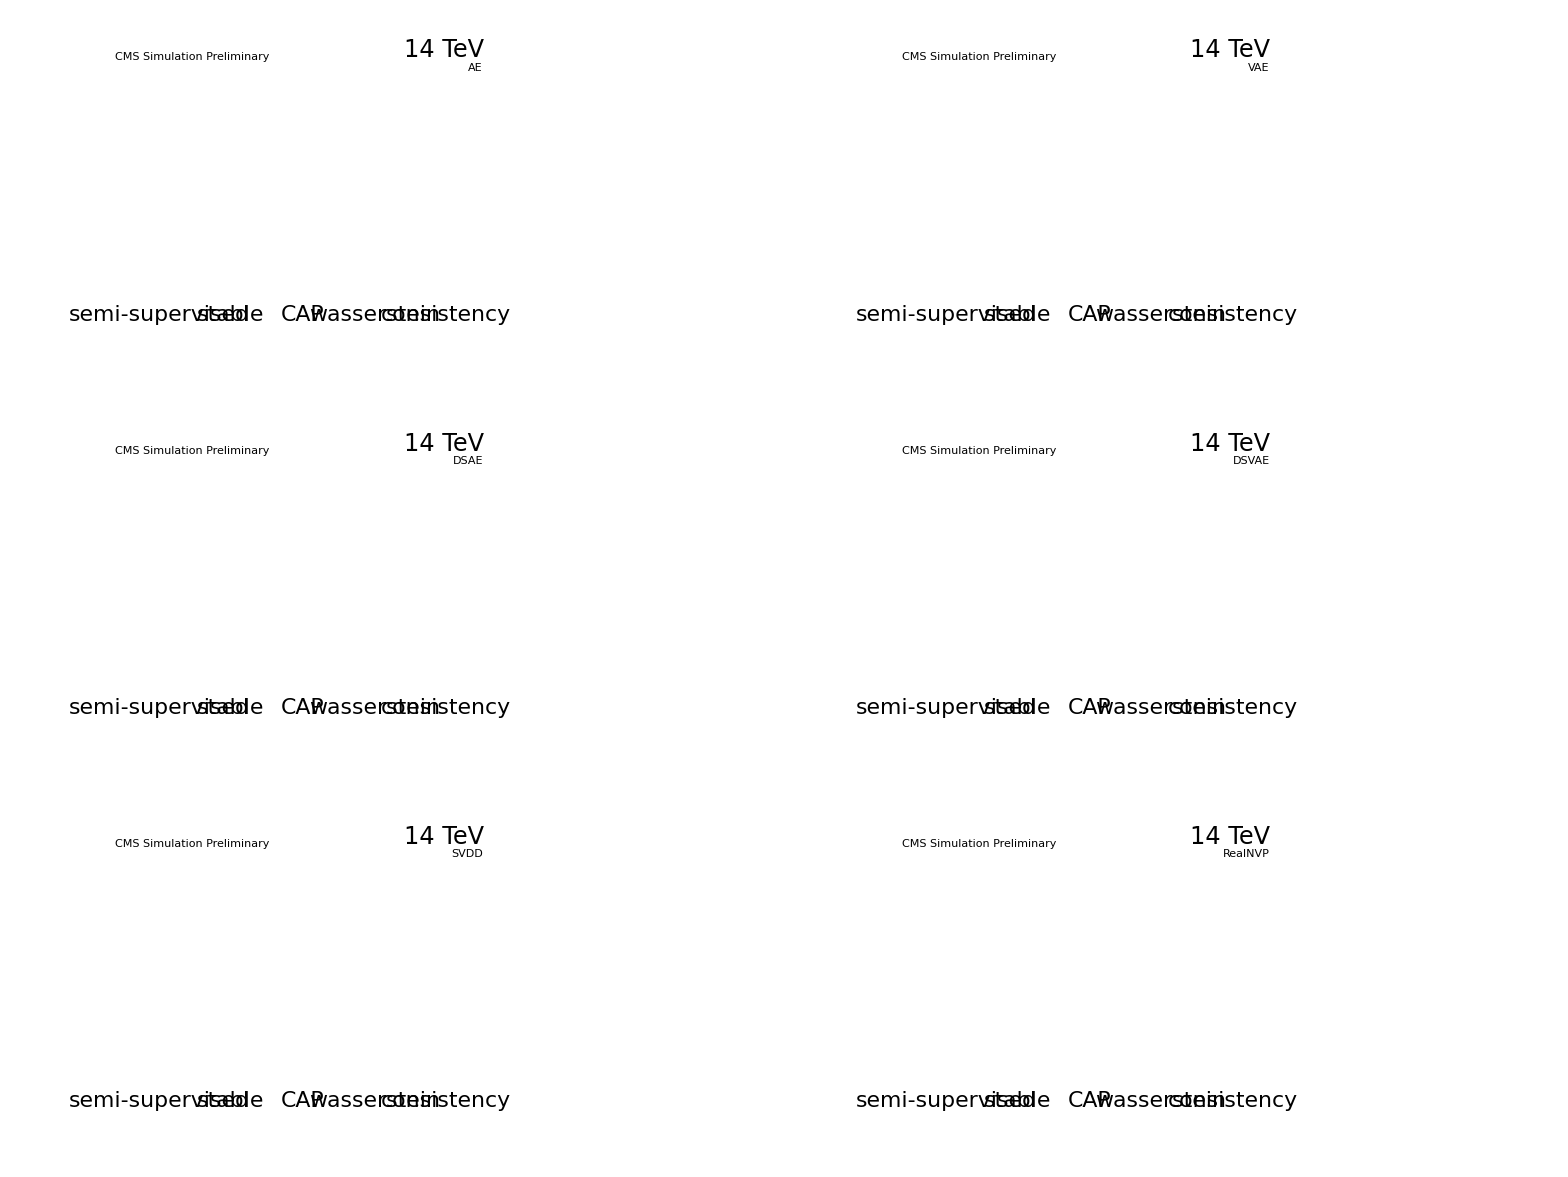

```mathematica
bestqPlot = makeRuleBoxGrid[dropEmptyModels[bestqGroups], 2]
Export[rebuttalOutDir <> "grouped_bestq" <> rebuttalTierSuffix <> ".svg", bestqPlot, "SVG"];
Export[rebuttalOutDir <> "grouped_bestq" <> rebuttalTierSuffix <> ".pdf", bestqPlot, "PDF"];
Export[rebuttalOutDir <> "grouped_bestq" <> rebuttalTierSuffix <> ".jpeg", bestqPlot, "JPEG"];
```

#### Q99 Comparison

```mathematica
bestqGroupsQ99 = rulePickArrays[rebuttalModelExpsQ99, bestQPick];
printTable[QuantileAxisLatex[toLegacyGroups[bestqGroups],
   toLegacyGroups[bestqGroupsQ99]]];
printTable[QuantileAxisMarkdown[toLegacyGroups[bestqGroups],
   toLegacyGroups[bestqGroupsQ99]]];
```

note: no harvest CSV for physics_dte_q99_pareto -- omitting this model.

\begin{tabular}{lcccccccccccc}
\toprule
 & \multicolumn{6}{c}{$q \approx 0.999991$ (250\,Hz)} & \multicolumn{6}{c}{$q = 0.99$} \\
Arch. & $\Delta_{\mathrm{C-C}}$ & $p$ & $\Delta_{\mathrm{C-S}}$ & $p$ & $\Delta_{\mathrm{C-W}}$ & $p$ & $\Delta_{\mathrm{C-C}}$ & $p$ & $\Delta_{\mathrm{C-S}}$ & $p$ & $\Delta_{\mathrm{C-W}}$ & $p$ \\
\midrule
AE & 3.85 & <0.001$^{*}$ & 2.44 & 0.002$^{*}$ & 2.98 & <0.001$^{*}$ & n/a & n/a & -6.23 & <0.001$^{*}$ & -11.42 & <0.001$^{*}$ \\
VAE & 0.01 & 0.001$^{*}$ & 0.96 & 0.064 & 0.01 & 1.000 & n/a & n/a & 8.87 & <0.001$^{*}$ & 8.80 & <0.001$^{*}$ \\
DSAE & 4.75 & 0.005$^{*}$ & 3.02 & 0.002$^{*}$ & 3.82 & 0.083 & n/a & n/a & -2.67 & <0.001$^{*}$ & -4.01 & <0.001$^{*}$ \\
DSVAE & -1.52 & 0.455 & 3.28 & <0.001$^{*}$ & 2.36 & 0.085 & n/a & n/a & 0.52 & 0.368 & 2.40 & 0.342 \\
SVDD & -2.31 & 0.840 & 0.82 & 0.455 & -5.70 & <0.001$^{*}$ & n/a & n/a & -23.84 & <0.001$^{*}$ & n/a & n/a \\
RealNVP & -3.27 & <0.001$^{*}$ & 0.01 & 1.000 & 0.31 & 1.000 & n/a & n/a & 0.84 & 0.342 & 5.30 & <0.001$^{*}$ \\
\bottomrule
\end{tabular}

| Arch. | d(C-C) tail | p | d(C-S) tail | p | d(C-W) tail | p | d(C-C) q99 | p | d(C-S) q99 | p | d(C-W) q99 | p |
|---|---|---|---|---|---|---|---|---|---|---|---|---|
| AE | 3.85 | <0.001* | 2.44 | 0.002* | 2.98 | <0.001* | n/a | n/a | -6.23 | <0.001* | -11.42 | <0.001* |
| VAE | 0.01 | 0.001* | 0.96 | 0.064 | 0.01 | 1.000 | n/a | n/a | 8.87 | <0.001* | 8.80 | <0.001* |
| DSAE | 4.75 | 0.005* | 3.02 | 0.002* | 3.82 | 0.083 | n/a | n/a | -2.67 | <0.001* | -4.01 | <0.001* |
| DSVAE | -1.52 | 0.455 | 3.28 | <0.001* | 2.36 | 0.085 | n/a | n/a | 0.52 | 0.368 | 2.40 | 0.342 |
| SVDD | -2.31 | 0.840 | 0.82 | 0.455 | -5.70 | <0.001* | n/a | n/a | -23.84 | <0.001* | n/a | n/a |
| RealNVP | -3.27 | <0.001* | 0.01 | 1.000 | 0.31 | 1.000 | n/a | n/a | 0.84 | 0.342 | 5.30 | <0.001* |

## Pareto Knee Selection

Rule: min-max normalise both recomputed objectives over the front and take the point furthest from the chord joining the endpoints (kneePick). Same tables, grid (grouped_knee_250Hz) and quantile axis as Best Q'.

#### 250 Hz

```mathematica
kneeGroups = rulePickArrays[rebuttalModelExps, kneePick];
kneeTabRows = HolmAdjustRows[BuildArchitectureRowsCompactCollapse[toLegacyGroups[kneeGroups], 10000, 0.05]];
printTable[LatexTableFromRows[kneeTabRows, 2]];
printTable[MarkdownTableFromRows[kneeTabRows, 2]];
```

#### Plots

```mathematica
kneePlot = makeRuleBoxGrid[dropEmptyModels[kneeGroups], 2]
Export[rebuttalOutDir <> "grouped_knee" <> rebuttalTierSuffix <> ".svg", kneePlot, "SVG"];
Export[rebuttalOutDir <> "grouped_knee" <> rebuttalTierSuffix <> ".pdf", kneePlot, "PDF"];
Export[rebuttalOutDir <> "grouped_knee" <> rebuttalTierSuffix <> ".jpeg", kneePlot, "JPEG"];
```

#### Q99 Comparison

```mathematica
kneeGroupsQ99 = rulePickArrays[rebuttalModelExpsQ99, kneePick];
printTable[QuantileAxisLatex[toLegacyGroups[kneeGroups],
   toLegacyGroups[kneeGroupsQ99]]];
printTable[QuantileAxisMarkdown[toLegacyGroups[kneeGroups],
   toLegacyGroups[kneeGroupsQ99]]];
```

## Spearman Ranking

Rank correlation between each strategy's Q' and the test efficiency over its front: rho (n) per architecture and strategy; no-pick = strategy absent, n/a = rho undefined.

```mathematica
printTable[spearmanMatrixLatex[rebuttalModelExps]];
printTable[spearmanMatrixMarkdown[rebuttalModelExps]];
```